```mathematica
(*vorts="vorts"<>ToString[#]&/@Range[99];*)
(*vorts="vorts"<>ToString[#]<>"_static"&/@Range[99];*)
(*vorts=("vorts"<>ToString[#]<>"_optimized_parallelsearch"&)/@Range[99];*)
dname="vorts";
index=1;
postfixes={"","_static","_optimized_parallelsearch"};
postfix=postfixes[[index]];
labels={": naive TF",": TF optimized for first frame",": TF optimized for each frame"};
label=labels[[index]];
vorts=(dname<>ToString[#]<>postfix&)/@Range[99];
```

```mathematica
path=NotebookDirectory[]<>"~images\\";
plotpath=NotebookDirectory[]<>"~plot\\";
datanames=(dname<>ToString[#]<>postfix&)/@Join[Range[1,23],Range[25,99]];
xml=Import[path<>First@datanames<>".xml"];
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname,plotpath,imagepath}=xml;
tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;
```

```mathematica
pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
(*features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];*)
chartcolors=rgbcolors[[#]]&/@index;

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];*)
(*Plot[fun[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
index0=Flatten@Position[alpha0,_?(#>0&)];
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98
1 | 0.428693 | 0.411928 | 0.393121 | 0.373258 | 0.354988 | 0.354941 | 0.338802 | 0.326271 | 0.3139 | 0.331926 | 0.349342 | 0.359217 | 0.362727 | 0.364164 | 0.385295 | 0.403735 | 0.403768 | 0.413818 | 0.418209 | 0.415862 | 0.406058 | 0.392429 | 0.371329 | 0.404219 | 0.401792 | 0.383796 | 0.38377 | 0.365164 | 0.373052 | 0.384283 | 0.402225 | 0.413333 | 0.412608 | 0.403495 | 0.390967 | 0.372796 | 0.356815 | 0.356867 | 0.35227 | 0.35422 | 0.351002 | 0.346207 | 0.337446 | 0.322706 | 0.316359 | 0.316431 | 0.309613 | 0.292381 | 0.292415 | 0.295865 | 0.309949 | 0.324346 | 0.339015 | 0.351841 | 0.362688 | 0.366713 | 0.362217 | 0.347577 | 0.325953 | 0.325968 | 0.31358 | 0.301451 | 0.319679 | 0.345635 | 0.372949 | 0.396615 | 0.419573 | 0.435178 | 0.443432 | 0.449884 | 0.449788 | 0.450745 | 0.443108 | 0.432198 | 0.410034 | 0.378637 | 0.343069 | 0.306319 | 0.27186 | 0.28674 | 0.316594 | 0.316609 | 0.343992 | 0.368237 | 0.388583 | 0.401502 | 0.409358 | 0.406504 | 0.400341 | 0.383277 | 0.358273 | 0.325453 | 0.325438 | 0.290259 | 0.27578 | 0.287204 | 0.287196 | 0.277257
2 | 0.091112 | 0.091217 | 0.0917485 | 0.0937281 | 0.0950763 | 0.0950215 | 0.0951107 | 0.0945406 | 0.0942239 | 0.0929833 | 0.0927913 | 0.0934409 | 0.0941997 | 0.0957801 | 0.0971746 | 0.097394 | 0.0974278 | 0.0971265 | 0.0973944 | 0.0977916 | 0.09902 | 0.100521 | 0.103778 | 0.101234 | 0.10166 | 0.10452 | 0.104482 | 0.106476 | 0.105218 | 0.103872 | 0.101349 | 0.0998483 | 0.100979 | 0.100948 | 0.101997 | 0.103327 | 0.103585 | 0.103569 | 0.102715 | 0.100951 | 0.100134 | 0.100571 | 0.101644 | 0.104095 | 0.105288 | 0.106239 | 0.10664 | 0.106863 | 0.106882 | 0.10821 | 0.107794 | 0.107338 | 0.106112 | 0.105867 | 0.104935 | 0.104235 | 0.105168 | 0.10705 | 0.108329 | 0.10832 | 0.107786 | 0.107904 | 0.108139 | 0.108513 | 0.10806 | 0.106479 | 0.103224 | 0.0995954 | 0.0961568 | 0.0935129 | 0.0935496 | 0.0919306 | 0.0930913 | 0.0950122 | 0.0995255 | 0.106804 | 0.113392 | 0.117331 | 0.11798 | 0.117832 | 0.115362 | 0.115396 | 0.111458 | 0.108915 | 0.105642 | 0.104434 | 0.102374 | 0.101111 | 0.10007 | 0.10011 | 0.101336 | 0.103746 | 0.103746 | 0.103884 | 0.104415 | 0.104675 | 0.105951 | 0.108316
3 | 0.0628314 | 0.0712607 | 0.080711 | 0.0895451 | 0.0985978 | 0.0985996 | 0.109385 | 0.119677 | 0.130402 | 0.116807 | 0.10366 | 0.096727 | 0.0939306 | 0.0911124 | 0.0745692 | 0.0635813 | 0.0634957 | 0.0577641 | 0.0573156 | 0.0586184 | 0.0624709 | 0.0693234 | 0.0789611 | 0.063063 | 0.0631821 | 0.0690159 | 0.0689572 | 0.0761485 | 0.0720209 | 0.0659636 | 0.0592916 | 0.0537287 | 0.0524954 | 0.0563606 | 0.0629488 | 0.0731053 | 0.0818454 | 0.0818665 | 0.0864467 | 0.0870816 | 0.0902238 | 0.0938262 | 0.0984296 | 0.105103 | 0.106599 | 0.104946 | 0.107875 | 0.118634 | 0.118628 | 0.114212 | 0.103571 | 0.0949891 | 0.0870448 | 0.0811545 | 0.0756225 | 0.0754724 | 0.0786775 | 0.0853807 | 0.096227 | 0.0962121 | 0.104019 | 0.11143 | 0.0983472 | 0.0826213 | 0.0672374 | 0.0546645 | 0.0464884 | 0.043594 | 0.0429347 | 0.0422013 | 0.042156 | 0.0432891 | 0.0461121 | 0.0487402 | 0.0544238 | 0.0639846 | 0.075656 | 0.090784 | 0.110366 | 0.100348 | 0.0864137 | 0.0864476 | 0.0745609 | 0.0666541 | 0.061091 | 0.0566395 | 0.0548312 | 0.0585894 | 0.0630037 | 0.0711805 | 0.0845818 | 0.101728 | 0.101749 | 0.124417 | 0.134217 | 0.122521 | 0.119047 | 0.122129

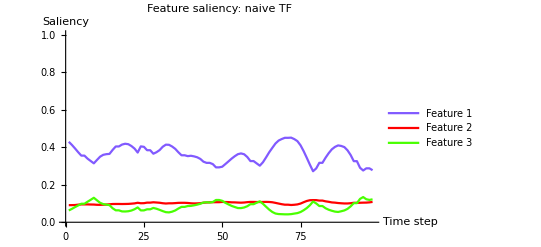

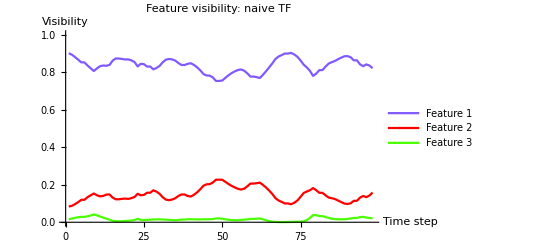

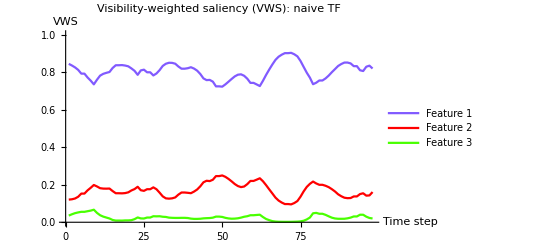

```mathematica
resultxml="D:\\document\\work\\time-varying-visualization\\~images\\saliency.xml";
scoremap=If[FileExistsQ[resultxml],Association@Import[resultxml],<||>];
features=Table[scoremap[#][[1]][[i]]&/@datanames,{i,Range[3]}];
TableForm[features,TableHeadings->Automatic]
ListLinePlot[features,PlotLegends->{"Feature 1","Feature 2","Feature 3"},PlotLabel->"Feature saliency"<>label,AxesLabel->{"Time step","Saliency"},PlotRange->{Automatic,{0,1}},PlotStyle->chartcolors]
ListLinePlot[Table[scoremap[#][[2]][[i]]&/@datanames,{i,Range[3]}],PlotLegends->{"Feature 1","Feature 2","Feature 3"},PlotLabel->"Feature visibility"<>label,AxesLabel->{"Time step","Visibility"},PlotRange->{Automatic,{0,1}},PlotStyle->chartcolors]
plot=ListLinePlot[Table[scoremap[#][[5]][[i]]&/@datanames,{i,Range[3]}],PlotLegends->{"Feature 1","Feature 2","Feature 3"},PlotLabel->"Visibility-weighted saliency (VWS)"<>label,AxesLabel->{"Time step","VWS"},PlotRange->{Automatic,{0,1}},PlotStyle->chartcolors]
Export[plotpath<>dname<>postfix<>".png",plot];
```

```mathematica
(*recordxml="D:\\document\\work\\time-varying-visualization\\~plot\\records.xml";
recordmap=If[FileExistsQ[recordxml],Association@Import[recordxml],<||>];
parallinesearch=recordmap[First@datanames][[4]][[3]]*)
```

```mathematica
(*tfinames=(plotpath<>#<>"_optimized_parallelsearch.tfi"&)/@datanames*)
```